```mathematica
(1/3 + 1/6)^2
```

1/4

```mathematica
3/(6/8)
```

4

```mathematica
Sin[Pi/2]
```

1

```mathematica
E^(Log[7])
```

7

```mathematica
Simplify[((3+4x)/(2+5x))^2+((2+x)/(1-x))^2]
```

(2+x)^2/(-1+x)^2+(3+4 x)^2/(2+5 x)^2

```mathematica
Simplify[x/y+y/x+2]
```

```mathematica
(x+y)^2/(x y)
Simplify[(x^2+y^2)^2-2(x y)^2]
```

(x+y)^2/(x y)

x^4+y^4

```mathematica
Simplify[Sin[x]^2  + Cos[x]^2]
```

1

```mathematica
FullSimplify[(Tan[Pi/8])^4+(Cot[Pi/8])^4]
```

34

```mathematica
FullSimplify[Sqrt[278+42*Sqrt[5]-12*Sqrt[6]-28*Sqrt[30]]]
```

3+7 √5-2 √6

```mathematica
Expand[(x+x y+y)^10]
```

x^10+10 x^9 y+10 x^10 y+45 x^8 y^2+90 x^9 y^2+45 x^10 y^2+120 x^7 y^3+360 x^8 y^3+360 x^9 y^3+120 x^10 y^3+210 x^6 y^4+840 x^7 y^4+1260 x^8 y^4+840 x^9 y^4+210 x^10 y^4+252 x^5 y^5+1260 x^6 y^5+2520 x^7 y^5+2520 x^8 y^5+1260 x^9 y^5+252 x^10 y^5+210 x^4 y^6+1260 x^5 y^6+3150 x^6 y^6+4200 x^7 y^6+3150 x^8 y^6+1260 x^9 y^6+210 x^10 y^6+120 x^3 y^7+840 x^4 y^7+2520 x^5 y^7+4200 x^6 y^7+4200 x^7 y^7+2520 x^8 y^7+840 x^9 y^7+120 x^10 y^7+45 x^2 y^8+360 x^3 y^8+1260 x^4 y^8+2520 x^5 y^8+3150 x^6 y^8+2520 x^7 y^8+1260 x^8 y^8+360 x^9 y^8+45 x^10 y^8+10 x y^9+90 x^2 y^9+360 x^3 y^9+840 x^4 y^9+1260 x^5 y^9+1260 x^6 y^9+840 x^7 y^9+360 x^8 y^9+90 x^9 y^9+10 x^10 y^9+y^10+10 x y^10+45 x^2 y^10+120 x^3 y^10+210 x^4 y^10+252 x^5 y^10+210 x^6 y^10+120 x^7 y^10+45 x^8 y^10+10 x^9 y^10+x^10 y^10

```mathematica
TrigExpand[Sin[x+y]]
```

Cos[y] Sin[x]+Cos[x] Sin[y]

```mathematica
a=3
b=4
c=6
o=a+b+c
s=o/2
Sqrt[s(s-a)(s-b)(s-c)]
```

3

4

6

13

13/2

(√455)/4

```mathematica
Clear[a,b,c,o,s]
```

```mathematica
s={3,2,0,0,5,13,2,-x,8}
s[[5]]
s[[-1]]
```

{3,2,0,0,5,13,2,-x,8}

5

8

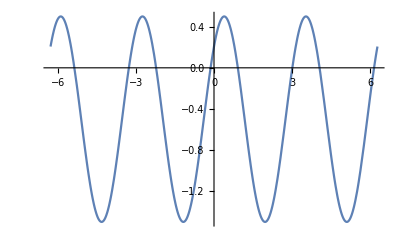

```mathematica
Plot[Sin[2x+Pi/4]-1/2,{x, -2Pi, 2Pi}]
```

-5 Sin[2-x]

-6+2^x

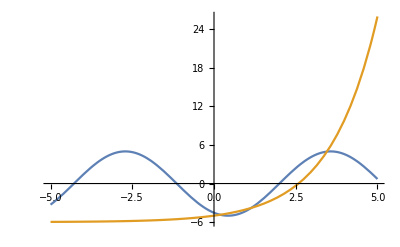

```mathematica
fx=5Sin[x-2]
gx=2^x-6
Plot[{fx, gx},{x, -5, 5}]
```

```mathematica
a=3^200+20
b=2^300+30
a==b
a<b
b<a
```

265613988875874769338781322035779626829233452653394495974574961739092490901302182994384699044021

2037035976334486086268445688409378161051468393665936250636140449354381299763336706183397406

False

False

True

```mathematica
Solve[x^2+4x+2==0,x]
```

{{x→-2-√2},{x→-2+√2}}

```mathematica
Solve[x^2+4x+5==0, x]
```

{{x→-2-ⅈ},{x→-2+ⅈ}}

```mathematica
Reduce[x^4==1, x]
```

x==-1||x==-ⅈ||x==ⅈ||x==1

```mathematica
Clear[fx, gx]
```

```mathematica
fx=(x^2-(x^2)^(1/3))E^x
```

ⅇ^x (x^2-(x^2)^(1/3))

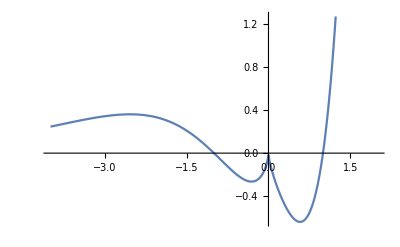

```mathematica
Plot[fx,{x, -4, 2}]
```

```mathematica
Solve[fx==0, x]
Reduce[fx==0, x]
```

{{x→0},{x→1}}

x==-1||x==0||x==1